{1.,0.,0.,0.,0.,0.,0.,0.}

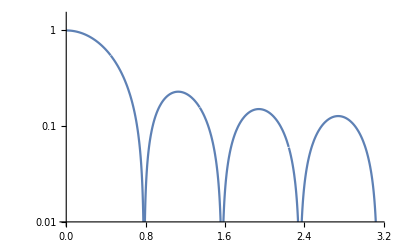

```mathematica
(* Create filter representation from Lagrange interpolation polynomials.
Note: H(e^jw) = h[0] + h[1]e^{-jw) + h[2]e^{-2jw} + h[3]e^{-3jw}.
Define: H_1(0) = 1, H_1(pi/3) = 0, H_1(2pi/3) = 0, H_1(pi) = 0.
Then project H_1 onto a fourier basis:
conj(F) . h[n] = H[e^jw] .:. h[n] = F . H[e^jw] = IFFT{H[e^jw]}, where H[e^jw] = {H[e^0], H[e^j\pi/2], H[e^j\pi], H^[e^j3\pi/2]} *)

(*H = {1, 1, 0, 1};*)
h0 =Sqrt[1/8] * InverseFourier[{1,0,0,0,0,0,0,0}];
h1 =Sqrt[1/8] * InverseFourier[{0,1,0,0,0,0,0,1}];
h2 =Sqrt[1/8] * InverseFourier[{0, 0, 1, 0,0,0,1,0}];
h3 =Sqrt[1/8] * InverseFourier[{0, 0, 0, 1,0,1,0,0}];
h4 =Sqrt[1/8] * InverseFourier[{0, 0, 0, 0,1,0,0,0}];
h0+h1+h2+h3+h4
LogPlot[Abs[ListFourierSequenceTransform[1.0h0+0.0h1+0.0h2, x]], {x, 0, Pi}, PlotRange->{10^-2, 1.4}]
```

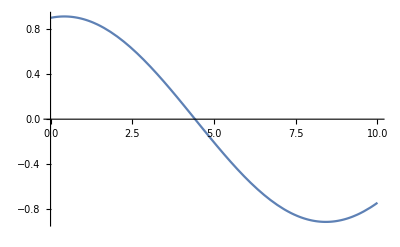

```mathematica
w = Pi/8;
Plot[h[[1]]*Cos[w*x] +h[[2]]*Cos[w (x-1)] +  h[[3]]*Cos[w(x-2)] + h[[4]]*Cos[w (x-3)], {x, 0, 10}]
```